## Set up

### Load Paclet

```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
Get["MathematicaSEAnalysis`"]
```

### Load processed EntityStore

This was generated in GatherMetadata.nb (watch out for the large number of shadowed symbols that need to be cleared):

```mathematica
SetDirectory[NotebookDirectory[]];
With[
{
store=Quiet@Import["mathematica.stackexchange.com_WithMetadata_2019-10-25_11-49-58.mx"]
},
ClearAll["Global`*"];
EntityUnregister/@store[];
EntityRegister[store]
]
```

{StackExchange.Mathematica:User,StackExchange.Mathematica:Badge,StackExchange.Mathematica:Comment,StackExchange.Mathematica:Post,StackExchange:PostType,StackExchange.Mathematica:Vote,StackExchange:VoteType,StackExchange.Mathematica:PostHistory,StackExchange:PostHistoryType,StackExchange:CloseReason,StackExchange.Mathematica:Tag}

### Helpful Definitions

```mathematica
ClearAll[NiceGrid];
NiceGrid[x_,opts___]:=Once[ResourceFunction["NiceGrid"]][Replace[x,{{}|<||>->{{}}}],opts];
```

## Find most commonly used symbols

### Gather data

```mathematica
symbolToCount=EntityValue["StackExchange.Mathematica:Post","WolframLanguageSymbols"]//Flatten//Counts//ReverseSort;
symbolToCount//Length
```

5126

```mathematica
symbolToCount[[;;10]]
```

<|List→213635,Times→162599,Set→146528,CompoundExpression→111586,Rule→108580,Plus→101682,Power→93773,Blank→69764,Pattern→66703,Function→61261|>

### Raw Data

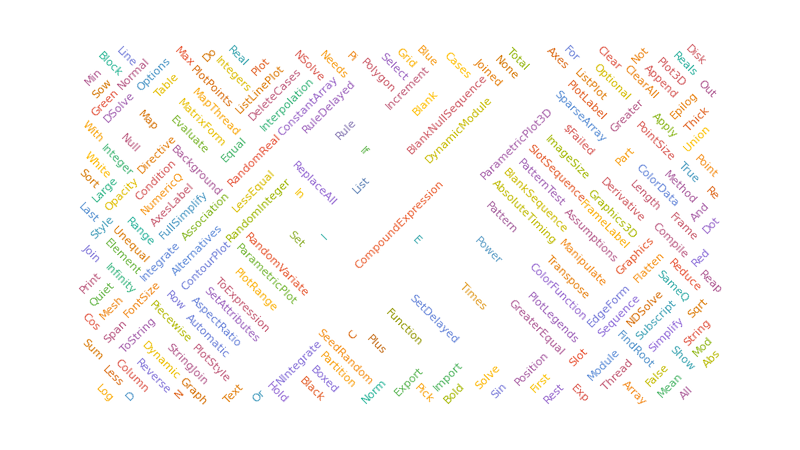

```mathematica
WordCloud[
symbolToCount[[;;200]],
MaxItems->Infinity,ScalingFunctions->"Log",
WordOrientation->{{π/4,7π/4}},WordSpacings->2,
AspectRatio->9/16,ImageSize->800
]
```

### Some common symbols removed

Remove some very common symbols to see more variety:

```mathematica
$VeryCommonSymbols={Entity["WolframLanguageSymbol","List"],Entity["WolframLanguageSymbol","Times"],Entity["WolframLanguageSymbol","CompoundExpression"],Entity["WolframLanguageSymbol","Set"],Entity["WolframLanguageSymbol","SetDelayed"],Entity["WolframLanguageSymbol","Null"],Entity["WolframLanguageSymbol","$Failed"],$Failed,Entity["WolframLanguageSymbol","Out"],Entity["WolframLanguageSymbol","In"]};
```

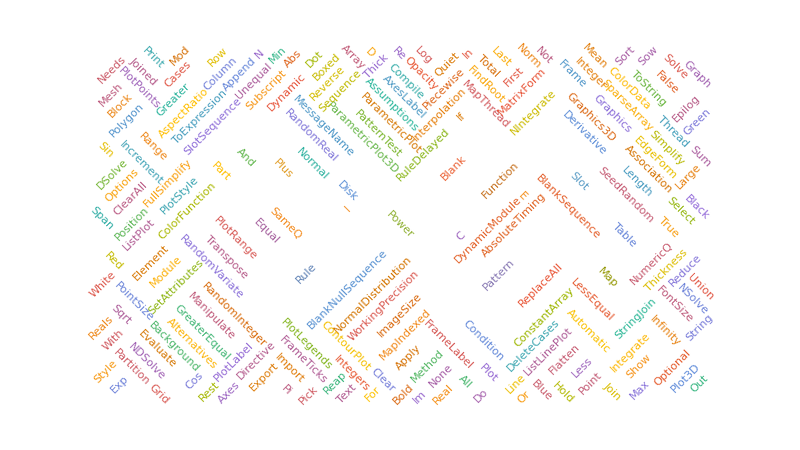

```mathematica
With[
{data=KeyDrop[symbolToCount,$VeryCommonSymbols][[;;200]]},
WordCloud[
data,
MaxItems->Length[data],
WordOrientation->{{π/4,7π/4}},
WordSpacings->2,
AspectRatio->9/16,
ImageSize->800,
ScalingFunctions->"Log"
]
]
```

### Compare symbol usage between two users

Remove even more commonly used symbols to better see differences:

```mathematica
$EvenMoreCommonSymbols=DeleteDuplicates@Join[$VeryCommonSymbols,{Entity["WolframLanguageSymbol","Rule"],Entity["WolframLanguageSymbol","Plus"],Entity["WolframLanguageSymbol","Power"],Entity["WolframLanguageSymbol","Blank"],Entity["WolframLanguageSymbol","Pattern"],Entity["WolframLanguageSymbol","Part"],Entity["WolframLanguageSymbol","Equal"],Entity["WolframLanguageSymbol","True"],Entity["WolframLanguageSymbol","False"],Entity["WolframLanguageSymbol","Slot"],Entity["WolframLanguageSymbol","Function"],Entity["WolframLanguageSymbol","Map"],Entity["WolframLanguageSymbol","ReplaceAll"],Entity["WolframLanguageSymbol","Table"],Entity["WolframLanguageSymbol","All"],Entity["WolframLanguageSymbol","Length"],Entity["WolframLanguageSymbol","Range"],Entity["WolframLanguageSymbol","Automatic"],Entity["WolframLanguageSymbol","None"]}];
```

Compare the word clouds side-by-side:

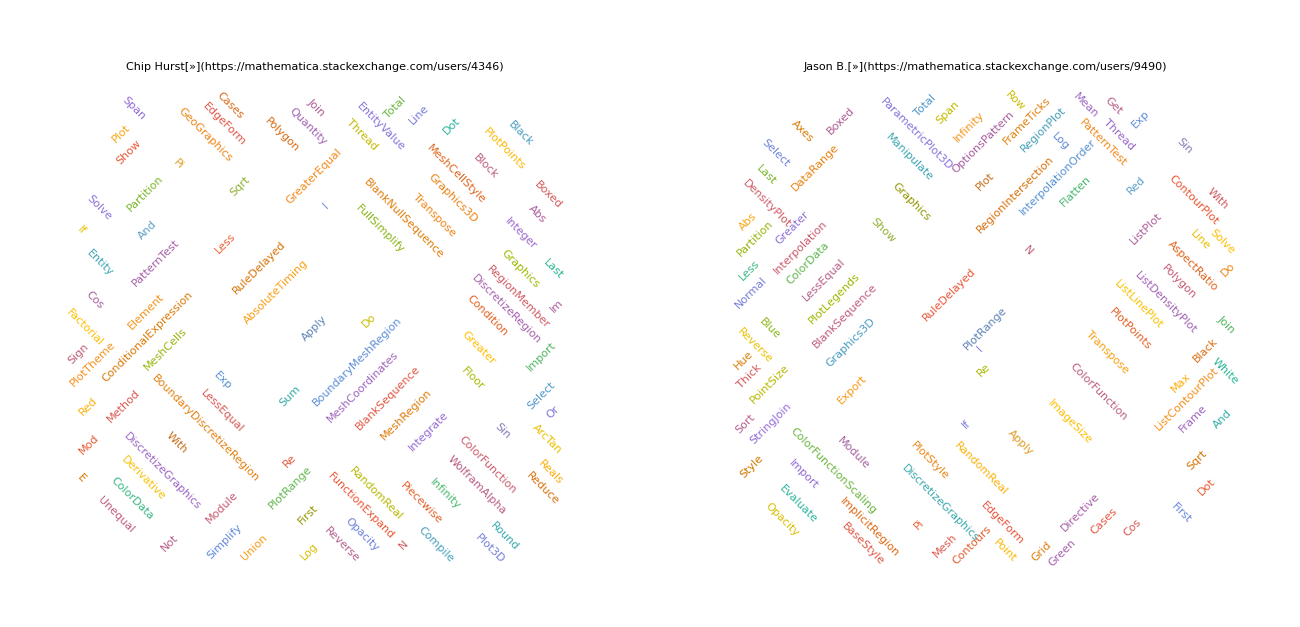

```mathematica
GraphicsGrid[
{
With[
{userSymbols=ReverseSort@Counts@Flatten@EntityClass["StackExchange.Mathematica:Post",{EntityProperty["StackExchange.Mathematica:Post","Owner"]->#}]["WolframLanguageSymbols"]},
WordCloud[KeyDrop[userSymbols,$EvenMoreCommonSymbols],WordOrientation->{{π/4,7π/4}},WordSpacings->2,PlotLabel->#,ScalingFunctions->"Log"]
]&/@{Entity["StackExchange.Mathematica:User","4346"],Entity["StackExchange.Mathematica:User","9490"]}
},
ImageSize->1300
]
```

## Adoption of Association after its Introduction

Association was not introduced into the Wolfram language until version 10, so there should not be many posts that use it prior to this date:

```mathematica
associationIntroDate=Entity["WolframLanguageSymbol","Association"]["DateIntroduced"]
```

Day: Wed 9 Jul 2014

### Gather data

Find the creation dates of all posts that use or mention Association:

```mathematica
associationPostDates=EntityValue[EntityClass["StackExchange.Mathematica:Post",{"WolframLanguageSymbols"->ContainsAny[{Entity["WolframLanguageSymbol","Association"]}]}],"CreationDate"];
associationPostDates//Length
```

2585

### Gather Version Release data

Gather some release date info for recent versions of the Wolfram Language from Stephen Wolfram's Blog:

```mathematica
versionToReleaseDate=Sort@<|
"V9"->DateObject[{2012, 11, 28}],
"V10"->DateObject[{2014, 7, 9}],
"V11"->DateObject[{2016, 8,8}],
"V12"->DateObject[{2019, 4,16}]
|>;
```

Process this information to determine the ranges when each version was the latest:

```mathematica
versionToDateBounds=AssociationThread[
Keys[versionToReleaseDate],
Transpose[
{
Values[versionToReleaseDate],
RotateLeft[Values[versionToReleaseDate]]
}
]/.{currentReleaseDate_DateObject,Min[versionToReleaseDate]}:>{currentReleaseDate,DateObject[{2020,1,1},"Day","Gregorian",-4.]}
]
```

<|V9→{Day: Wed 28 Nov 2012,Day: Wed 9 Jul 2014},V10→{Day: Wed 9 Jul 2014,Day: Mon 8 Aug 2016},V11→{Day: Mon 8 Aug 2016,Day: Tue 16 Apr 2019},V12→{Day: Tue 16 Apr 2019,Day: Wed 1 Jan 2020}|>

Gather Spikey icons for each version from MathWorld:

```mathematica
versionToSpikey=AssociationThread[{"V9","V10","V11","V12"}->{-Graphics-,-Graphics-,-Graphics-,-Graphics-}];
```

### Visualize monthly posts created mentioning Association

Show the monthly post counts alongside when each recent version of the Wolfram Language was released.
Note that many posts were created fairly soon after the release of version 10, and that the average number of posts had increased and stabilized during the version 11 release cycle, indicating that users are indeed using Association.

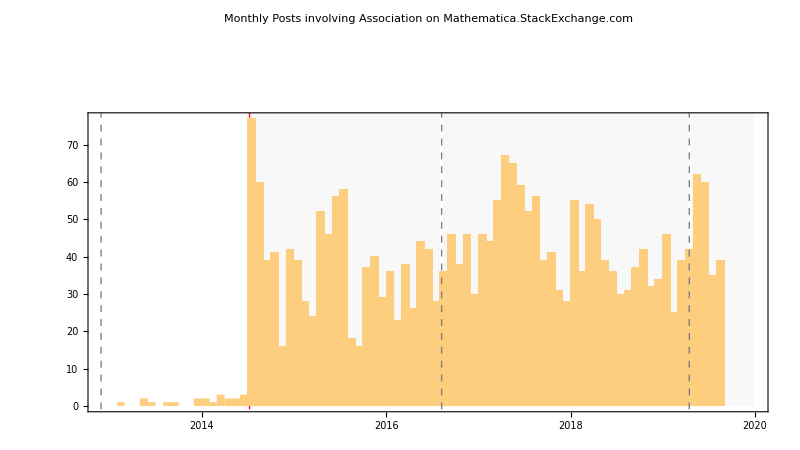

```mathematica
DateHistogram[associationPostDates,"Month",
Prolog->{
KeyValueMap[
With[
{xCoords=#2},
{
{If[#1==="V10",Directive[Red,Thick],Gray],Dashed,InfiniteLine[{{#,0},{#,1}}]&[Min[xCoords]]},
{Opacity[1],Text[Style[#1,FontSize->18,FontColor->Black,FontWeight->Bold],{(Min[xCoords]+(DateDifference@@xCoords)/2),95}]},
{Inset[versionToSpikey[#1],{(Min[xCoords]+(DateDifference@@xCoords)/2),80}]},
If[#1=!="V9",
{Opacity[0.05,Gray],Rectangle[{xCoords[[1]]+Quantity[1,"Weeks"],0},{xCoords[[2]]-Quantity[1,"Weeks"],102}]},
{}
]
}
]&,
versionToDateBounds
]
},
PlotTheme->"Detailed",
PlotRangePadding->{Automatic,{Automatic,Scaled[.25]}},
AspectRatio->9/16,
PlotLabel->"Monthly Posts involving Association on Mathematica.StackExchange.com",
ImageSize->800,
LabelStyle->18,
PlotRange->{MinMax[versionToDateBounds],Automatic}
]
```

#### Zoom in on 2014

Looking closer at the release date of version 10, we can see that there are a few posts that prematurely use Association.
This may be due to many factors, such as early exposure to power users at the annual Wolfram Technology Conference, or posts being edited after their creation to use or mention Association.

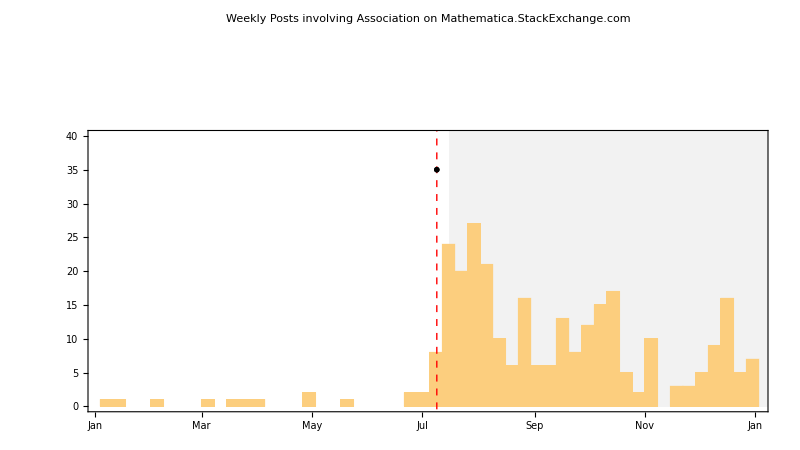

```mathematica
zoomedInAssociaitonPostDates=Select[associationPostDates,DateWithinQ[DateObject[{2014}],#]&];
DateHistogram[zoomedInAssociaitonPostDates,"Week",
Prolog->{
{{{Directive[RGBColor[1, 0, 0],Thickness[Large]],Dashing[{Small,Small}],InfiniteLine[{{DateObject[{2014,7,9},"Day","Gregorian",-4.],0},{DateObject[{2014,7,9},"Day","Gregorian",-4.],1}}]},{Opacity[1],Text["V10",{DateObject[{2014,7,9},"Day","Gregorian",-4.],50},{-3.5,-0.75}]},{Inset[-Graphics-,{DateObject[{2014,7,9},"Day","Gregorian",-4.],35},Scaled[{-0.12,0}]]},{Opacity[0.1,GrayLevel[0.5]],Rectangle[{DateObject[{2014,7,16},"Day","Gregorian",-4.],0},{DateObject[{2016,8,1},"Day","Gregorian",-4.],53.5}]}}},
{{{Opacity[1],Text["V9",{DateObject[{2014,7,9},"Day","Gregorian",-4.],50},{7,-0.75}]},{Inset[-Graphics-,{DateObject[{2014,7,9},"Day","Gregorian",-4.],35},Scaled[{1.25,0}]]}(*{Opacity[0.1,GrayLevel[0.5]],Rectangle[{DateObject[{2014,1,4,16,3,32},"Instant","Gregorian","UTC"],0},{DateObject[{2014,7,2},"Day","Gregorian",-4.],53.5}]}*)}}
},
PlotTheme->"Detailed",
PlotRangePadding->{Automatic,{Automatic,Scaled[.25]}},
AspectRatio->9/16,
PlotLabel->"Weekly Posts involving Association on Mathematica.StackExchange.com",
ImageSize->800,
LabelStyle->18,
PlotRange->{MinMax[zoomedInAssociaitonPostDates],{0,40}}

]
```